```mathematica
m2=1;
L=10;
tf=10;
```

```mathematica
Xi[x_,y_,z_]=Exp[(-((x-L/2)^2+(y-L/2)^2+(z-L/2)^2))/(2(L/10)^2)];
```

```mathematica
DensityPlot3D[Xi[x,y,z],{x,0,L},{y,0,L},{z,0,L}]
```

-Graphics3D-

```mathematica
sol=NDSolve[{D[D[X[t,x,y,z], t], t]==D[D[X[t,x,y,z], x], x]+D[D[X[t,x,y,z], y], y]+D[D[X[t,x,y,z], z], z]-m2 X[t,x,y,z],X[0,x,y,z]==Xi[x,y,z],D[X[t,x,y,z], t]==0/.{t->0},X[t,L,y,z]==X[t,0,y,z],X[t,x,L,z]==X[t,x,0,z],X[t,x,y,L]==X[t,x,y,0]},{X[t,x,y,z]},{t,0,tf},{x,0,L},{y,0,L},{z,0,L}][[1]];
```

NDSolve::mxsst: Using maximum number of grid points 22 allowed by the MaxPoints or MinStepSize options for independent variable x.

NDSolve::mxsst: Using maximum number of grid points 22 allowed by the MaxPoints or MinStepSize options for independent variable y.

NDSolve::mxsst: Using maximum number of grid points 22 allowed by the MaxPoints or MinStepSize options for independent variable z.

General::stop: Further output of NDSolve::mxsst will be suppressed during this calculation.

```mathematica
Xsol[t_,x_,y_,z_]=X[t,x,y,z]/.sol;
```

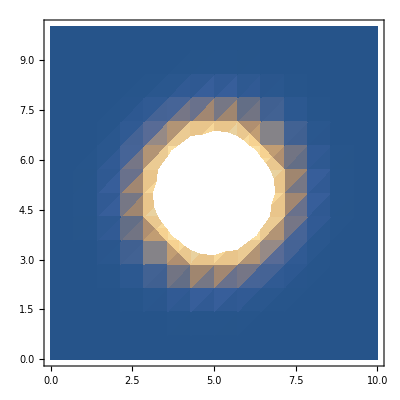
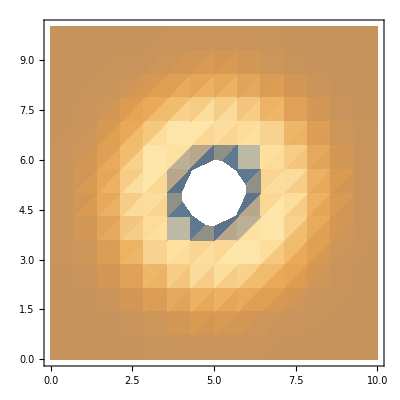
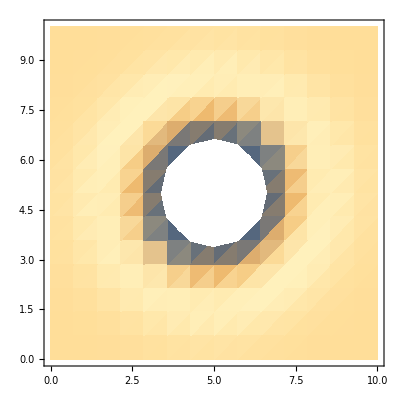
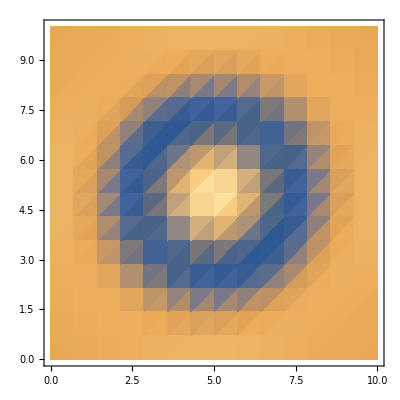
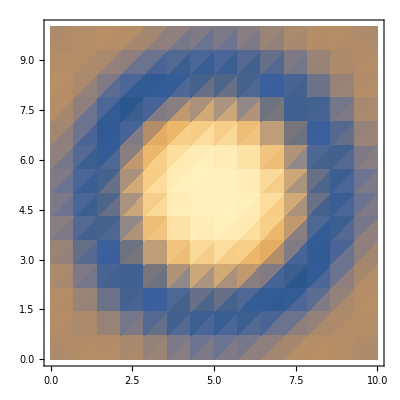
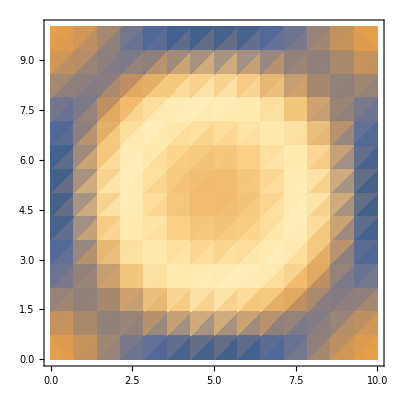
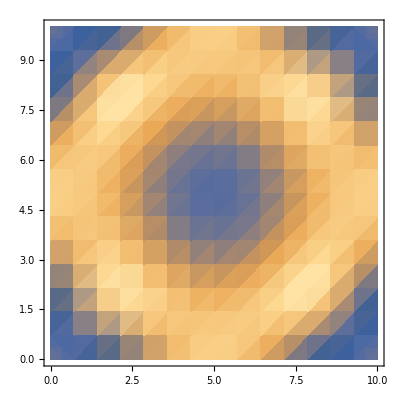
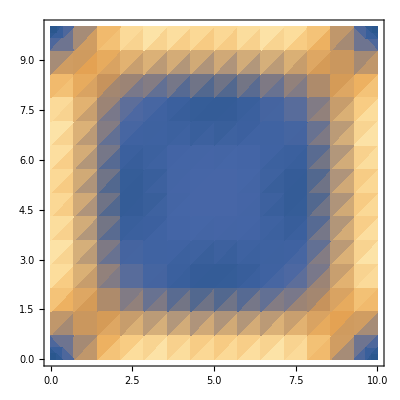

```mathematica
Table[DensityPlot[Xsol[t,x,y,L/2],{x,0,L},{y,0,L}],{t,0,tf}]
```